# Error mitigation via extrapolation

Reference: quant-ph/2011.01382

## Richardson extrapolation

For simplicity, consider that each gate has the same error rate ϵ. Then the expectation value of some observable M is a function of ϵ. Let’s Taylor-expand this function around ϵ=0:
⟨M⟩(ϵ)=⟨M⟩(0)+∑_(k=1)^n M_k ϵ^k+𝒪(ϵ^(n+1))

```mathematica
M[ϵ_,n_]:=M[0]+∑_(k=1)^n Subscript[M, k] ϵ^k
```

Let’s say we have measured the expectation ⟨M⟩ at n+1 different error rates
⟨M(α_k ϵ)⟩, k∈(0,...,n) ,
where
1=α_0<α_1<...<α_n .
With these n+1 different measurements we can fix all coefficients of the Taylor-series up to order ϵ^n. That is, we can solve for
⟨M⟩(0), M_1, M_2,...,M_n .
Our estimate for the noiseless expectation value is then ⟨M⟩(0).

## Example: n=1

We measure
⟨M⟩(α_0 ϵ), ⟨M⟩(α_1 ϵ)
where α_0=1 and fit
⟨M⟩(0), M_1 .

```mathematica
Solve[{M[Subscript[α, 0] ϵ]==M[Subscript[α, 0] ϵ,1],M[Subscript[α, 1] ϵ]==M[Subscript[α, 1] ϵ,1]},{M[0],Subscript[M, 1]}]//Expand
```

{{M[0]→(M[ϵ α_1] α_0)/(α_0-α_1)-(M[ϵ α_0] α_1)/(α_0-α_1),M_1→M[ϵ α_0]/(ϵ (α_0-α_1))-M[ϵ α_1]/(ϵ (α_0-α_1))}}

Therefore,
⟨M⟩(0)=α_1/(α_1-α_0)⟨M⟩(α_0 ϵ)+α_0/(α_0-α_1)⟨M⟩(α_1 ϵ) + 𝒪(ϵ^2) .

#### Depolarizing noise

Consider measuring X on the state ρ=|+⟩⟨+| under a depolarizing noise channel
ℰ(ρ)=ϵ/2 I+(1-ϵ)ρ .
The expectation values are measured for α_0=1 and α_1=2.

```mathematica
noise[ρ_,ϵ_]:=ϵ/2 IdentityMatrix[2]+(1-ϵ)ρ
(state=KroneckerProduct[{1,1}/(√2),{1,1}/(√2)])//MatrixForm
X=PauliMatrix[1];
```

(1/2 | 1/2
1/2 | 1/2)

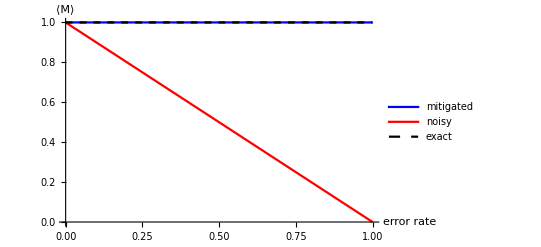

```mathematica
Plot[{2Tr[X.noise[state,ϵ]]-Tr[X.noise[state,2ϵ]],Tr[X.noise[state,ϵ]],Tr[X.state]},{ϵ,0,1},AxesLabel->{"error rate","⟨M⟩"},PlotLegends->{"mitigated","noisy","exact"},PlotStyle->{Blue,Red,{Black,Dashed}}]
```

This was boring so let’s try something else.

#### Amplitude damping

```mathematica
noise[ρ_,ϵ_]:=({{1, 0}, {0, √(1-ϵ)}}).ρ.({{1, 0}, {0, √(1-ϵ)}})+({{0, √ϵ}, {0, 0}}).ρ.({{0, 0}, {√ϵ, 0}})
```

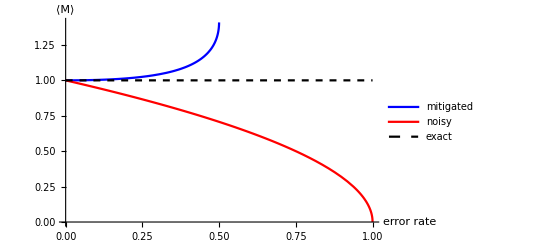

```mathematica
Plot[{2Tr[X.noise[state,ϵ]]-Tr[X.noise[state,2ϵ]],Tr[X.noise[state,ϵ]],Tr[X.state]},{ϵ,0,1},AxesLabel->{"error rate","⟨M⟩"},PlotLegends->{"mitigated","noisy","exact"},PlotStyle->{Blue,Red,{Black,Dashed}}]
```

## General n

In general the mitigated estimate for ⟨M⟩(0) is
⟨M⟩(0)=∑_(k=0)^n β_k⟨M⟩(α_k ϵ) ,
where
β_k=∏_(i≠k) α_i/(α_k-α_i) .

## Estimate variance

For general n, the estimated expectation value is a linear combination of random variables. In general for two random variables the following holds
Var(a X+b Y)=a^2 Var (X)+b^2 Var(Y) .
Therefore
Var(⟨M⟩(0))=∑_(k=0)^n β_k^2 Var(⟨M⟩(α_k ϵ)) .
This is γ=∑_(k=0)^n β_k^2 times larger than Var(⟨M⟩), assuming the variances on the right hand side are approximately constant. Therefore, we have to take γ-times more samples to have the same variance as we would have without Richardson extrapolation. γ is known as the sampling cost or cost of error mitigation. Also, apparently γ increases exponentially in n so only small constant values of n are practical.